# ColorGraphVertices

Color the vertices in a graph with no adjacent vertices sharing a color

## Definition

```mathematica
ClearAll[ColorGraphVertices]
ColorGraphVertices[graph_?GraphQ,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{VertexStyle->Thread[VertexList[graph]->FindVertexColoring[graph,ColorData[106,"ColorList"]]]}],options];

ColorGraphVertices[graph_?GraphQ,colors_List,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{VertexStyle->Thread[VertexList[graph]->FindVertexColoring[graph,colors]]}],options]
```

## Documentation

### Usage

ColorGraphVertices[graph]

colors the vertices of graph with no adjacent vertices having the same color.

ColorGraphVertices[graph, colors]

uses colors from the color list colors.

### Details & Options

Every planar graph can have colors assigned to its vertices such that no adjacent vertices have the same color with at most four colors according to the four color theorem.

The vertices are colored using ColorData[106] by default.

Deciding whether a graph can be colored with 3 or more colors is NP complete.

## Examples

### Basic Examples

Color the vertices of the Petersen graph:

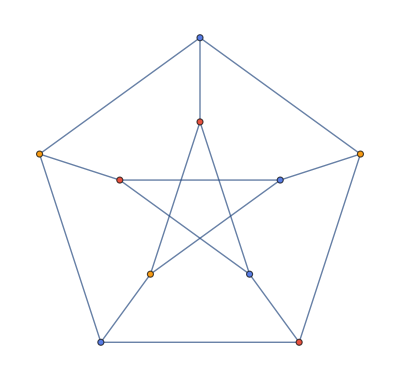

```mathematica
ColorGraphVertices[PetersenGraph[]]
```

Color the vertices of the Petersen graph with color list 105:

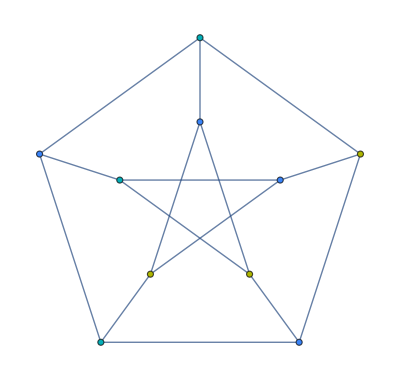

```mathematica
ColorGraphVertices[PetersenGraph[],ColorData[105,"ColorList"]]
```

Color the vertices of the Petersen graph with a random sample of crayola colors:

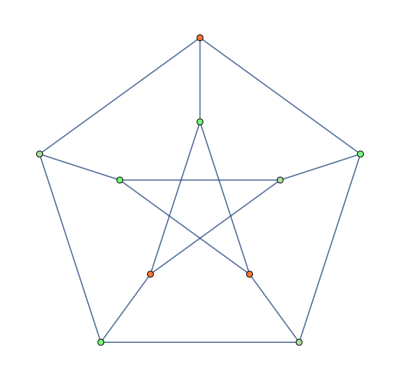

```mathematica
ColorGraphVertices[PetersenGraph[],RandomSample[ColorData["Crayola","ColorList"]]]
```

Color the vertices of the Menger sponge graph:

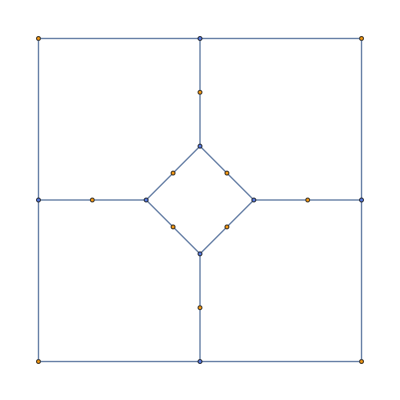

```mathematica
ColorGraphVertices[GraphData[{"MengerSponge", 1}]]
```

Color the vertices of the Pappus Graph:

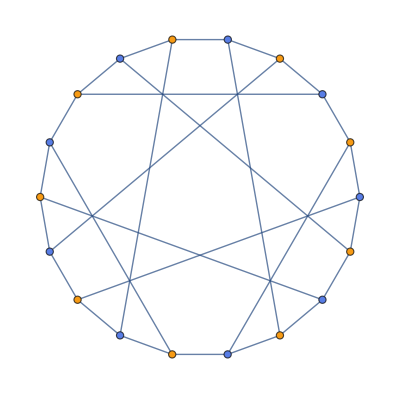

```mathematica
ColorGraphVertices[GraphData["PappusGraph"]]
```

Color the vertices of the Coxeter graph:

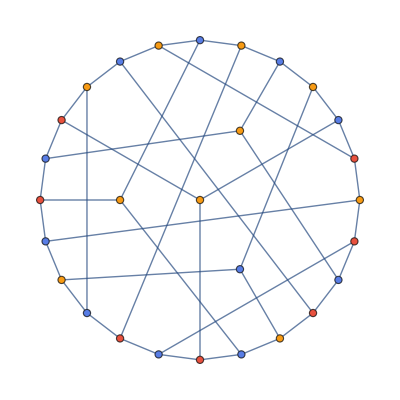

```mathematica
ColorGraphVertices[GraphData["CoxeterGraph"]]
```

Color the vertices of the Tutte 12-cage graph:

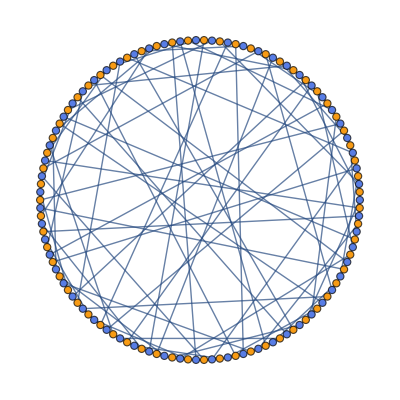

```mathematica
ColorGraphVertices[GraphData["Tutte12Cage"]]
```

### Options

Specify a graph option:

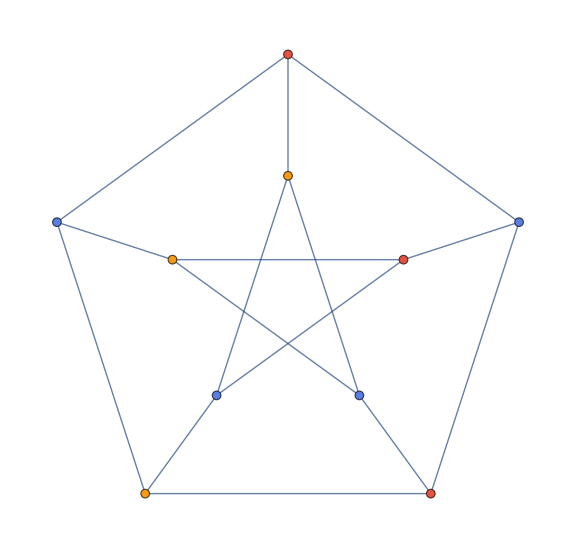

```mathematica
ColorGraphVertices[PetersenGraph[],ImageSize->Large]
```

### Applications

Color the vertices of the skeleton of the Csaszar polyhedron:

```mathematica
ColorGraphVertices[MeshConnectivityGraph[PolyhedronData["CsaszarPolyhedron","Polyhedron"],0]]
```

-Graphics3D-

Make a large random graph and color the vertices:

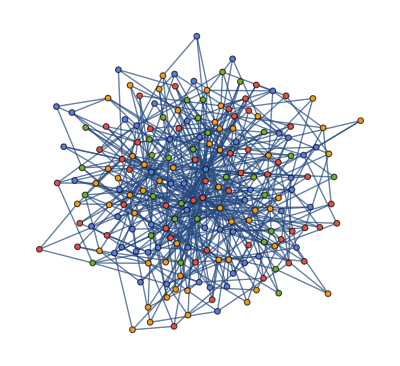

```mathematica
ColorGraphVertices[RandomGraph[BarabasiAlbertGraphDistribution[192,3]],ImageSize->Full]
```

### Properties & Relations

Make a 3D buckyball graph with colors:

```mathematica
Graph3D[ColorGraphVertices[BuckyballGraph[]]]
```

-Graphics3D-

Make a 3D torus graph with colors:

```mathematica
Graph3D[ColorGraphVertices[TorusGraph[{4,4,4}]]]
```

-Graphics3D-

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

four color theorem

chromatic number

graph coloring

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FindVertexColoring

VertexStyle

FindIndependentEdgeSet

FindEdgeColoring

### Related Resource Objects

ColorGraphEdges

FoldGraph

TriangularGridGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

A node is a vertex. The function could also be named ColorGraphVertices but I prefer ColorGraphNodes because it is shorter and a node does not have a different plural form like vertex/vertices.ColorGraphVertices

Vertex is the standard term used in the language (cf. VertexList, VertexCount, etc.), so naming this ColorGraphVertices helps with consistency. Please reconsider your name choice.

I have reconsidered and will rename the function.

I also added more examples.